Reference: email chain “Quantum Information in quantum cognition: Framework and applications” -- message sent by Elizabeth on 6/17/18
“I attached some Mathematica code that I used to compute the Posner binding rates.   Since this work involved a lot of exploration, it’s basically a wall of code that shows how I compute a few examples of Posner binding.  And then from there I would run it in interpreter mode, building Posner configurations and applying the binding projector to them.”

Some comments added by ABW

```mathematica
Clear[ω];
dot[{v1_,v2_,v3_},{v4_,v5_,v6_}]:= Dot[v1,v4]+Dot[v2,v5]+Dot[v3,v6] 
(* Just defining a normal dot product*)
z = SparseArray@{{1,0},{0,-1}};plus = 1/(√2){1,1};minus = 1/(√2){1,-1}; eye = 1/(√2){1,ⅈ};meye=1/(√2){1,-ⅈ};u = {1,0};d={0,1};
(* And defining some standard states *)
x =  SparseArray@{{0,1},{1,0}};y = SparseArray@{{0,-ⅈ},{ⅈ,0}};i=IdentityMatrix[2];
(* Also operators *)
X[k_]:= If[k==0,IdentityMatrix[64],KroneckerProduct@@ReplacePart[(i&/@Range[6]),k->x/2]];
Y[k_]:= If[k==0,IdentityMatrix[64],KroneckerProduct@@ReplacePart[(i&/@Range[6]),k->y/2]];
Z[k_]:= If[k==0,IdentityMatrix[64],KroneckerProduct@@ReplacePart[(i&/@Range[6]),k->z/2]];
(* 6fold product of X/Y/Z operators*)
sriff[x_]:= StringJoin@@(ToString/@x)
kp[x__] := Flatten@KroneckerProduct[x];
vec2str[vec__,dim_]:= Simplify@Total@Table[
digits = PadLeft[IntegerDigits[r,2],Log[2,dim]];
vr = kp@@(digits/.{0->u,1->d});
vr.vec sriff[digits],{r,0,dim-1}]
c3 =Table[
If[PadLeft[IntegerDigits[x,2],3]==Permute[PadLeft[IntegerDigits[y,2],3],Cycles[{{3,1,2}}]],1,0],{x,0,7},{y,0,7}];
c6 =Table[
If[PadLeft[IntegerDigits[x,2],6]==Permute[PadLeft[IntegerDigits[y,2],6],Cycles[{{3,1,2},{6,4,5}}]],1,0],{x,0,63},{y,0,63}];
tp = KroneckerProduct;
swap[p_,q_]:= tp@@ReplacePart[(i&/@Range[6]),{p->tp[u,u],q->tp[u,u]}]+ tp@@ReplacePart[(i&/@Range[6]),{p->tp[d,u],q->tp[u,d]}]+ tp@@ReplacePart[(i&/@Range[6]),{p->tp[u,d],q->tp[d,u]}] +  tp@@ReplacePart[(i&/@Range[6]),{p->tp[d,d],q->tp[d,d]}]
u = SparseArray@{1,0};d = SparseArray@{0,1}; i = SparseArray@IdentityMatrix[2];
bp = 1/(√2)SparseArray@(kp[u,d]-kp[d,u]); 
(* here the basis for a single triangle of 3 qubits is encoded by hand, together with a database
of its quantum numbers.  Some of it is just for printing tables and so on and isn't part of the math. *)
svals={{3/2,3/2,1},{3/2,1/2,1},{3/2,-1/2,1},{3/2,-3/2,1},{1/2,1/2,ω},{1/2,1/2,ω^2},{1/2,-1/2,ω},{1/2,-1/2,ω^2}};
m8= {kp[u,u,u],1/(√3)(kp[u,u,d]+kp[u,d,u]+kp[d,u,u]),1/(√3)(kp[d,d,u]+kp[d,u,d]+kp[u,d,d]),kp[d,d,d],1/(√3)(kp[u,u,d]+ω kp[u,d,u]+ω^2 kp[d,u,u]),1/(√3)(kp[u,u,d]+ω^2 kp[u,d,u]+ω kp[d,u,u]),1/(√3)(kp[d,d,u]+ω kp[d,u,d]+ω^2 kp[u,d,d]),1/(√3)(kp[d,d,u]+ω^2 kp[d,u,d]+ω kp[u,d,d])};
st = SparseArray/@(Flatten[Table[kp[m8[[i]],m8[[j]]],{i,8},{j,8}],1]/.{ω^3->1,ω^4->ω});
nm = {"000",W,OverBar[W],"111",ω,ω^2,OverBar[ω],OverBar[ω^2]};
(*name*)
bits =Numerator/@vec2str[#,8]&/@m8//Expand;
names=Flatten[Table[AngleBracket[nm[[i]],nm[[j]]],{i,8},{j,8}],1];
tauvals=Flatten[Table[svals[[i,3]]svals[[j,3]],{i,8},{j,8}]]/.ω->Exp[ⅈ π 2/3];
t0=Flatten@Position[tauvals,1];
t1=Flatten@Position[tauvals,ⅇ^((2 ⅈ π)/3)];
t2=Flatten@Position[tauvals,ⅇ^(-(2 ⅈ π)/3)];

sp=Flatten[Table[{svals[[i,1]]⊗svals[[j,1]],svals[[i,2]],svals[[j,2]],svals[[i,2]]+svals[[j,2]],svals[[i,3]]⊗svals[[j,3]],AngleBracket[nm[[i]],nm[[j]]]},{i,8},{j,8}],1];
plus = 1/(√2){1,1};minus = 1/(√2){1,-1};rp =1/(√2)(kp[plus,d]-kp[minus,u]); 
swap[p_,q_]:= tp@@ReplacePart[(i&/@Range[6]),{p->tp[u,u],q->tp[u,u]}]+ tp@@ReplacePart[(i&/@Range[6]),{p->tp[d,u],q->tp[u,d]}]+ tp@@ReplacePart[(i&/@Range[6]),{p->tp[u,d],q->tp[d,u]}] +  tp@@ReplacePart[(i&/@Range[6]),{p->tp[d,d],q->tp[d,d]}]
R[θ_]:= SparseArray@{{Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}}
ω=Exp[ⅈ 2 π/3];
stt = Table[kp[st[[k]],st[[r]]],{k,64},{r,64}];
ptt =Table[tp[Conjugate[stt[[k,r]]],stt[[k,r]]],{k,64},{r,64}];

t00=Table[{k, r},{k,t0},{r,t0}];
t01=Table[{k, r},{k,t0},{r,t1}];
t02=Table[{k, r},{k,t0},{r,t2}];

t10=Table[{k, r},{k,t1},{r,t0}];
t11=Table[{k, r},{k,t1},{r,t1}];
t12=Table[{k, r},{k,t1},{r,t2}];

t20=Table[{k, r},{k,t2},{r,t0}];
t21=Table[{k, r},{k,t2},{r,t1}];
t22=Table[{k, r},{k,t2},{r,t2}];

pb= Sum[ptt[[Sequence@@count]],{count,Flatten[Join[t00,t12,t21],1]}];  (*projector onto the binding subspace *)
pnb=Sum[ptt[[Sequence@@count]],{count,Flatten[Join[t01,t02,t10,t11,t20,t22],1]}]; (*projector onto the not binding subspace *)
p00=Sum[ptt[[Sequence@@count]],{count,Flatten[t00,1]}];
p01=Sum[ptt[[Sequence@@count]],{count,Flatten[t01,1]}];
p02=Sum[ptt[[Sequence@@count]],{count,Flatten[t02,1]}];
p10=Sum[ptt[[Sequence@@count]],{count,Flatten[t10,1]}];
p11=Sum[ptt[[Sequence@@count]],{count,Flatten[t11,1]}];
p12=Sum[ptt[[Sequence@@count]],{count,Flatten[t12,1]}];
p20=Sum[ptt[[Sequence@@count]],{count,Flatten[t20,1]}];
p21=Sum[ptt[[Sequence@@count]],{count,Flatten[t21,1]}];
p22=Sum[ptt[[Sequence@@count]],{count,Flatten[t22,1]}];
```

```mathematica
(* this part defines several states of two Posners as density matrices over the standard bais.
The idea is to first take a tensor product of qubits 1...12 with the correct number of Bell
pairs, but on the wrong qubits (because bell pairs can only occupy consecutive slots when we write them
into slots 1...12).  Then to fix these wrong qubit labels the code applies some number of swap gates to relabel the qubits, 
and this transfers the entanglement appropriately. *)

swap[p_,q_]:= tp@@ReplacePart[(i&/@Range[12]),{p->tp[u,u],q->tp[u,u]}]+ tp@@ReplacePart[(i&/@Range[12]),{p->tp[d,u],q->tp[u,d]}]+ tp@@ReplacePart[(i&/@Range[12]),{p->tp[u,d],q->tp[d,u]}] +  tp@@ReplacePart[(i&/@Range[12]),{p->tp[d,d],q->tp[d,d]}]
initStateA= KroneckerProduct[1/2 i,1/2 i,1/2 i,1/2 i,1/2 i,1/2 i,1/2 i,1/2 i,1/2 i,1/2 i,1/2 i,1/2 i];
initStateBB= KroneckerProduct[1/2 i,1/2 i,tp[bp,bp],1/2 i,tp[bp,bp],1/2 i,tp[bp,bp],1/2 i,1/2 i];
initStateBBB= KroneckerProduct[tp[bp,bp],1/2 i,1/2 i,1/2 i,1/2 i,tp[bp,bp],1/2 i,1/2 i,1/2 i,1/2 i];
initStateB= KroneckerProduct[tp[bp,bp],tp[bp,bp],1/2 i,tp[bp,bp],1/2 i,tp[bp,bp],tp[bp,bp]];
initStateB2= KroneckerProduct[tp[bp,bp],tp[bp,bp],1/2 i,1/2 i,1/2 i,1/2 i,tp[bp,bp],tp[bp,bp]];

initStateB3= KroneckerProduct[tp[bp,bp],1/2 i,1/2 i,tp[bp,bp],tp[bp,bp],1/2 i,1/2 i,tp[bp,bp]];
initStateB4= KroneckerProduct[tp[bp,bp],tp[bp,bp],tp[bp,bp],tp[bp,bp],tp[bp,bp],tp[bp,bp]];
initStateB4b= swap[4,9].KroneckerProduct[tp[bp,bp],tp[bp,bp],tp[bp,bp],tp[bp,bp],tp[bp,bp],tp[bp,bp]].Transpose[swap[4,9]];
initStateC=swap[6,11].swap[4,9].swap[2,7]. KroneckerProduct[tp[bp,bp],tp[bp,bp],tp[bp,bp],tp[bp,bp],tp[bp,bp],tp[bp,bp]].Transpose[swap[6,11].swap[4,9].swap[2,7]];
initStateCC=swap[6,11].swap[4,9]. KroneckerProduct[tp[bp,bp],tp[bp,bp],tp[bp,bp],tp[bp,bp],tp[bp,bp],tp[bp,bp]].Transpose[swap[6,11].swap[4,9]];
initStateB=swap[6,11].swap[4,9]. KroneckerProduct[1/2 i,1/2 i,tp[bp,bp],tp[bp,bp],1/2 i,1/2 i,tp[bp,bp],tp[bp,bp]].Transpose[swap[6,11].swap[4,9]];

initStateCCCb=swap[6,11].swap[4,9]. KroneckerProduct[tp[bp,bp],tp[bp,bp],tp[bp,bp],tp[bp,bp],tp[bp,bp],tp[bp,bp]].Transpose[swap[6,11].swap[4,9]];
initStateD=swap[5,6].KroneckerProduct[1/2 i,1/2 i,1/2 i,1/2 i,1/2 i,tp[bp,bp],1/2 i,1/2 i,1/2 i,1/2 i,1/2 i].Transpose[swap[5,6]];

initState6=swap[5,12].swap[4,9].  KroneckerProduct[1/2 i,1/2 i,tp[bp,bp],tp[bp,bp],1/2 i,1/2 i,1/2 i,1/2 i,1/2 i,1/2 i].Transpose[swap[5,12].swap[4,9]];
```

```mathematica
(*"Taumography" gives the relevant probabilities of finding the Posner in each Tau sector*)
```

```mathematica
pTau = List[p00,p01,p02,p10,p11,p12,p20,p21,p22];
Taumography[state_] := Table[Tr[(pTau[[k]]).state],{k,1,9}]
```

```mathematica
(* Sample calculation below. Init state C is the state shown in Fig 1 of the main paper*)
```

```mathematica
Taumography[initStateC] // Simplify
```

{3/8,0,0,0,0,5/16,0,5/16,0}

```mathematica
(* And now we define a version of init state C with a single spin rotated *)
```

```mathematica
Rz[theta_] := SparseArray[{{1,1} -> 1, {2,2} -> Exp[I theta]}]
Rot[theta_] :=tp[i,Rz[theta]]
```

```mathematica
RotC[theta_] :=swap[6,11].swap[4,9].swap[2,7]. KroneckerProduct[Rot[theta].tp[bp,bp].Rot[-theta],tp[bp,bp],tp[bp,bp],tp[bp,bp],tp[bp,bp],tp[bp,bp]].Transpose[swap[6,11].swap[4,9].swap[2,7]];
```

```mathematica
(* Taumograph on posners with a range of rotation angles *)
```

```mathematica
TaumographyTable = {}
```

{}

```mathematica
(* This step should take a while. Computation results are saved and loaded below *)
```

```mathematica
For[j=0, j < 101, j++, TaumographyTable =  Append[TaumographyTable, Taumography[RotC[2Pi j/100]]] ;Print[j]]
```

0

1

2

3

$Aborted

```mathematica
TaumographyTable
```

{{3/8+27/8 (1/27+1/27 ⅇ^(-(2 ⅈ π)/3)+1/27 ⅇ^((2 ⅈ π)/3)),5/48+5/48 ⅇ^(-(2 ⅈ π)/3)+5/48 ⅇ^((2 ⅈ π)/3)+27/8 (1/27+1/27 ⅇ^(-(2 ⅈ π)/3)+1/27 ⅇ^((2 ⅈ π)/3)),5/48+5/48 ⅇ^(-(2 ⅈ π)/3)+5/48 ⅇ^((2 ⅈ π)/3)+27/8 (1/27+1/27 ⅇ^(-(2 ⅈ π)/3)+1/27 ⅇ^((2 ⅈ π)/3)),5/48+5/48 ⅇ^(-(2 ⅈ π)/3)+5/48 ⅇ^((2 ⅈ π)/3)+27/8 (1/27+1/27 ⅇ^(-(2 ⅈ π)/3)+1/27 ⅇ^((2 ⅈ π)/3)),5/48+5/48 ⅇ^(-(2 ⅈ π)/3)+5/48 ⅇ^((2 ⅈ π)/3)+27/8 (1/27+1/27 ⅇ^(-(2 ⅈ π)/3)+1/27 ⅇ^((2 ⅈ π)/3)),5/16+27/8 (1/27+1/27 ⅇ^(-(2 ⅈ π)/3)+1/27 ⅇ^((2 ⅈ π)/3)),5/48+5/48 ⅇ^(-(2 ⅈ π)/3)+5/48 ⅇ^((2 ⅈ π)/3)+27/8 (1/27+1/27 ⅇ^(-(2 ⅈ π)/3)+1/27 ⅇ^((2 ⅈ π)/3)),5/16+27/8 (1/27+1/27 ⅇ^(-(2 ⅈ π)/3)+1/27 ⅇ^((2 ⅈ π)/3)),5/48+5/48 ⅇ^(-(2 ⅈ π)/3)+5/48 ⅇ^((2 ⅈ π)/3)+27/8 (1/27+1/27 ⅇ^(-(2 ⅈ π)/3)+1/27 ⅇ^((2 ⅈ π)/3))},{19/72+5,8},98,{3/8+27/8 (1/27+1/27 ⅇ^(-(2 ⅈ π)/3)+1/27 ⅇ^((2 ⅈ π)/3)),7,5/48+5/48 ⅇ^(-(2 11π)/3)+5/48 ⅇ^(1/3)+27/8 (1/27+1/27 ⅇ^(-(2 ⅈ π)/3)+1/27 ⅇ^((2 ⅈ π)/3))}}
 |  |  |  |

```mathematica
Export["TaumographyTable.mx",TaumographyTable]
```

TaumographyTable.mx

```mathematica
TaumographyTable = Import["TaumographyTable.mx"];
```

```mathematica
(* Small imaginary parts in some values. I think a computational artifact. Cleaned out here *)
```

```mathematica
TaumographyTable = Re[TaumographyTable//Simplify];
```

```mathematica
Export["SimplifiedTaumographyTable.mx",TaumographyTable]
```

SimplifiedTaumographyTable.mx

```mathematica
(* Compute overlap with desired Tau sector. Results plotted below *)
```

```mathematica
OddProb = Table[3/8 * Total[TaumographyTable[[j]][[{2,3,4,7}]]] + 5/16*Total[TaumographyTable[[j]][[{2,3,4,7}]]]+10/16*Total[TaumographyTable[[j]][[{5,9}]]] ,{j,1,101}];
ModOddProb = Table[Total[TaumographyTable[[j]][[{2,3,4,7}]]]  ,{j,1,101}];
```

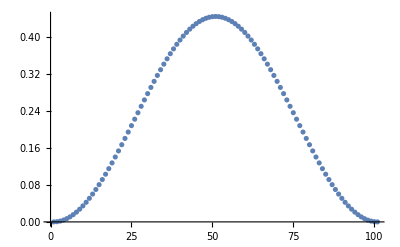

```mathematica
ListPlot[OddProb]
```

```mathematica
ListPlot[ModOddProb]
```

-Graphics-

```mathematica
Length[Angles]
```

101

```mathematica
EvenProb = 1 - OddProb;
Angles = Table[2 Pi j/100,{j,0,100}];
PPoints = Transpose[{Angles,EvenProb}];
```

```mathematica
(*Plot from the paper *)
```

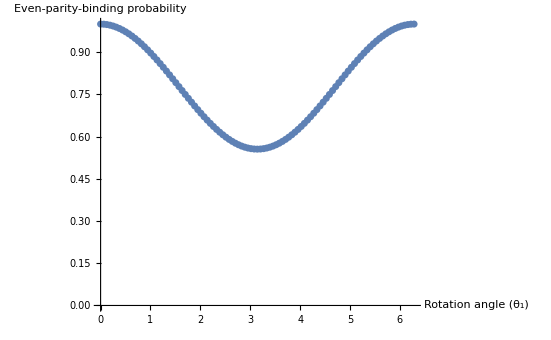

```mathematica
ListPlot[PPoints, AxesLabel ->{"Rotation angle (θ_1)", "Even-parity-binding probability"},PlotRange->{{0,2Pi},{0,1}}]
```